Open Loop

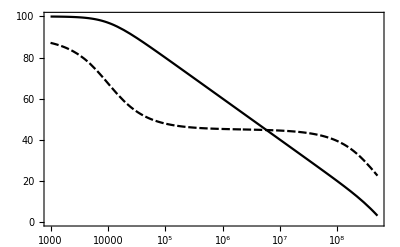

Ideal Loop

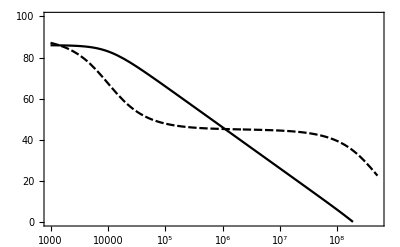

Real Loop

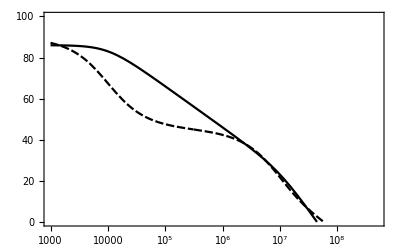

Comped Loop

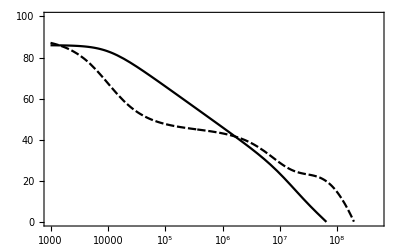

```mathematica
AD0=100000;p0=10000;p1=500*10^6;
p2=10*10^6;delay=1*10^-9;
Rf=1000;Rg=250;
AD[s_]:=AD0/((1+s/p0)(1+s/p1));
AL[s_]:=AD[s]*Rg/(Rf+Rg);
AL1[s_]:=AL[s]/(1+s/p2)*ⅇ^(-s delay);
Cc=32*10^-12;
Par[x_,y_]:=(x*y)/(x+y);
AL2[s_]:=AL1[s]*(s Rf Cc+1)/(s Par[Rf,Rg]Cc+1);
mybode=Function[{tf,ω0,ω1,db0,db1,ph0,ph1},
LogLinearPlot[{
20*Log10[Abs[tf[ⅈ ω]]],
(180/π*Arg[tf[ⅈ ω]]-ph0)/(ph1-ph0)*(db1-db0)+db0
},{ω,ω0,ω1},PlotRange->{db0,db1},PlotTheme->"Monochrome",GridLines->Automatic,Frame->True
] //Print;
];
Print["Open Loop"];
mybode[AD,1000,500000000,0,100,-180,20]
Print["Ideal Loop"];
mybode[AL,1000,500000000,0,100,-180,20]
Print["Real Loop"];
mybode[AL1,1000,500000000,0,100,-180,20]
Print["Comped Loop"];
mybode[AL2,1000,500000000,0,100,-180,20]
```

```mathematica
TransferFunctionModel
```

```mathematica
Rf=.;Cf=.;Rg=.;
Zf[s_]:=(Rf*1/(s Cf))/(Rf+1/(s Cf));
Simplify[Zf[s]/Rg]
```

Rf/(Rg+Cf Rf Rg s)